This is a notebook acompanying the file rec_2D_line.tex

```mathematica
NotebookDirectory[]<>"ellipse.m" // Get
```

```mathematica
(*NotebookDirectory[]<>"CorrelatedGauss.m" // Get*)
```

```mathematica
NotebookDirectory[]<>"detector.m" // Get
```

```mathematica
Clear[P]
```

```mathematica
SetDirectory@FileNameJoin@{NotebookDirectory[],"..","doc","figures"}
```

```mathematica
toProjectionSpaceTan[{y_,z_,t_},R_]:={z+ (R-y)t, z- (R+y) t,-2 y Sqrt[t^2+1]}
toProjectionSpaceTheta[{y_,z_,θ_},R_]:=toProjectionSpaceTan[{y,z,Tan[θ]},R]
```

```mathematica
LabeledArrow[{begin_,end_},text_]:={Arrowheads[{-.025,.025}],Arrow[{begin,end}],Text[text,1/2(begin+end),Background->White]}
```

```mathematica
drawDetector[{R_,L_}]:=Module[{},
{Line[{{-L/2,R},{L/2,R}}],Line[{{-L/2,-R},{L/2,-R}}]}
]
```

```mathematica
draw2DAxes[c_,{a1_,l1_,t1_,s1_ : 0.1 },{a2_,l2_,t2_, s2_ : 0.1}]:=Module[{},
{Thickness[0.001], Dashing[0.01], Arrow[{c-s1  l1 a1,c+a1 l1}], Arrow[{c-s2  l2 a2,c+a2 l2}]}
]
```

```mathematica
drawEvent[{y_,z_,θ_},R_]:=Module[{zu,zd,dl,m},
{zu,zd,dl}= toProjectionSpaceTheta[{y,z,θ},R];
{Line[{{zu,R},{zd,-R}}],{Red,PointSize[0.025],Point[{z,y}]}}
]
```

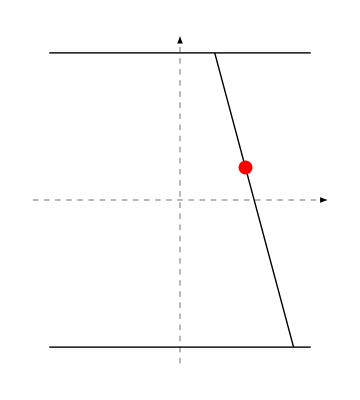

```mathematica
detector={drawDetector[{450,800}], draw2DAxes[{0,0},{{1,0},450,"z",1},{{0,1},500,"y",1}],drawEvent[{100,200,-15 Degree},450]}//Graphics
```

```mathematica
Export["detector.eps",detector,"EPS"]
```

detector.eps

```mathematica
resolution={10,50,0}
```

{10,50,0}

```mathematica
fromProjectionSpaceTan[{zu_,zd_,dl_},R_]:=Module[{t,y,z},
t=(zu-zd)/(2R);
y=-1/2 dl/Sqrt[1+t^2];
z = 1/2 (zu+zd+2 y t);
{y,z,t}
]
fromProjectionSpaceTheta[{zu_,zd_,dl_},R_]:=Module[{t,y,z},
t=(zu-zd)/(2R);
y=-1/2 dl/Sqrt[1+t^2];
z = 1/2 (zu+zd+2 y t);
{y,z,ArcTan[t]}
]
```

```mathematica
toProjectionSpaceTan[fromProjectionSpaceTan[{-200,300,100},450],450]//Simplify
```

{-200,300,100}

```mathematica
toProjectionSpaceTheta[fromProjectionSpaceTheta[{-200,300,20 Degree},450],450]//Simplify
```

{-200,300,20 °}

```mathematica
aVec[{y_,z_,θ_},R_]:={y-R, y+R, 2 y Sin[θ]}
```

```mathematica
bVec[{y_,z_,θ_},{dy_,dz_},R_]:={-dz +dy Tan[θ],-dz +dy Tan[θ],2 dy/Cos[θ]}
```

```mathematica
correlationMatrix[{sz_,sl_,η_}]={{sz^2,0,η},{0,sz^2,-η},{η,-η,sl^2}}
```

{{sz^2,0,η},{0,sz^2,-η},{η,-η,sl^2}}

```mathematica
iC[{sz_,sl_,η_}]:=Inverse[correlationMatrix[{sz,sl,η}]]
```

```mathematica
dtmin[{sz_,sl_,η_},{ty_,tz_,tθ_},{dy_,dz_},R_]:=Module[{b,a,ic},
ic=iC[{sz,sl,η}];
b=bVec[{ty,tz,tθ},{dy,dz},R];
a=aVec[{ty,tz,tθ},R];
b.ic.a/a.ic.a
]
```

```mathematica
gaussian[{sz_,sl_,η_},{ty_,tz_,tθ_},{dy_,dz_},R_]:=Module[{b,a,ic},
ic=iC[{sz,sl,η}];
b=bVec[{ty,tz,tθ},{dy,dz},R];
a=aVec[{ty,tz,tθ},R];
1/2 (b.ic.b - (b.ic.a)^2/a.ic.a)
]
```

```mathematica
approximateP[s_,meas_,{y_,z_},R_]:=Module[{ic,a,b,diff,tmin},
ic=iC[s];
a=aVec[meas,R];
diff={y-meas[[1]],z-meas[[2]]};
b=bVec[meas,diff,R];

tmin=Tan[meas[[3]] ]+dtmin[s,meas,diff,R];
Sqrt[Det[ic]/a.ic.a]/(2Pi^2) 1/(1+tmin^2) Exp[-gaussian[s,meas,diff,R]]
]
```

```mathematica
errorFunction[meas_,{y_,z_},s_,R_,t_]:= Module[{f,err,true},
true=toProjectionSpaceTan[{y,z,t},R];
err= meas-true;
f=1/2 err.iC[s].err
]
```

```mathematica
P[s_,meas_,{y_,z_,θ_},R_]:= Module[{f,ic},
ic=iC[s];
f=errorFunction[toProjectionSpaceTheta[meas,R],{y,z},s,R,Tan[θ]];
Sqrt[Det[ic]]/Sqrt[2 Pi]^3 Exp[-f]
]
```

```mathematica
P[s_,meas_,{y_,z_},R_]:= Module[{f,ic},
NIntegrate[P[s,meas,{y,z,θ},R],{θ,-Pi/2,Pi/2}]/Pi
]
```

```mathematica
NIntegrate[P[resolution,fromProjectionSpaceTheta[{zu,zd,dl},450],{0,0,30Degree},450],{zu,-500,500},{zd,-500,500},{dl, -750,750}]
```

1.

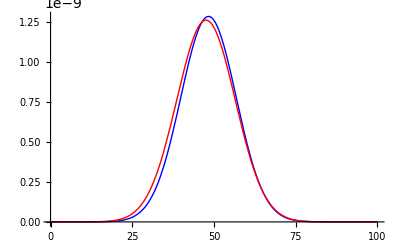

```mathematica
Plot[{approximateP[resolution,{300,0,45Degree},{350,z},450],P[resolution,{300,0,45Degree},{350,z},450],ev[350,z]},{z,0,100},PlotStyle->{Blue,Red,Green},PlotRange->All]
```

```mathematica
Plot[{ev[350,z]/P[resolution,{300,0,45Degree},{350,z},450]},{z,0,100},PlotStyle->{Blue,Red},PlotRange->All]
```

-Graphics-

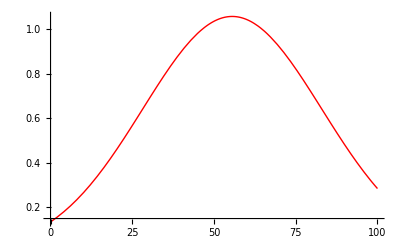

```mathematica
Plot[{approximateP[resolution,{300,0,45Degree},{350,z},450]/P[resolution,{300,0,45Degree},{350,z},450]},{z,0,100},PlotStyle->{Blue,Red},PlotRange->All]
```

```mathematica
compare[s_,meas_,{y_,z_},R_]:=Module[{e,a},
e=P[s,meas,{y,z},R];
a=approximateP[s,meas,{y,z},R];
{e,a,a-e,(a-e)/e}//N]
```

```mathematica
compare[resolution,{0,0,15 Degree},{0,0},450]
```

{1.48521×10^-7,1.48546×10^-7,2.50452×10^-11,0.000168631}

```mathematica
compare[resolution,{300,0,45 Degree},{350,50},450]
```

{1.21609×10^-9,1.26072×10^-9,4.46336×10^-11,0.0367026}

```mathematica
coeffs[form_,{x_,y_}]:= {Coefficient[form,x^2],Coefficient[form,y^2],Coefficient[form,x y]/2}
```

```mathematica
caseStudy[s_,meas_,R_]:=Module[{el,g,y,z,a,b,c,p={meas[[2]],meas[[1]]},limits},
g=gaussian[s,meas,{y,z},R];
{a,b,c}=coeffs[g,{z,y}]//N;
Print[a," " ,b," ",c];
el=reconstructEllipse[a,b,c,1];
el;
limits=ellipseLimits[a,b,c,1];
{{drawDetector[{450,300}],drawEvent[meas,R],ellipse[p,a,b,c,1],ellipse[p,a,b,c,3],
{Thin,ellipseBoundingBox[a,b,c,3,{meas[[2]],meas[[1]]},Gray]},
Line[{p-{1,3} limits ,p+{-1,3}limits}],
Line[{p-{0,3} limits ,p+{0,3}limits}],
Line[{p-{-1,3} limits ,p+{1,3}limits}],
Line[{p-{3,1}limits,p+{3,-1}limits}],
Line[{p-{3,0}limits,p+{3,0}limits}],
Line[{p-{3,-1}limits,p+{3,1}limits}]
}//Graphics,

GraphicsGrid[{Table[Plot[{P[s,meas,{meas[[1]]+q limits[[2]],z},R],approximateP[s,meas,{meas[[1]]+q limits[[2]],z},R]},{z, meas[[2]]-3limits[[1]],meas[[2]]+3limits[[1]]},PlotRange->All,PlotStyle->{Red,Blue}],{q,-1,1}],
Table[Plot[{P[s,meas,{y,meas[[2]]+q limits[[1]]},R],approximateP[s,meas,{y,meas[[2]]+q limits[[1]]},R]},{y, meas[[1]]-3limits[[2]],meas[[1]]+3limits[[2]]},PlotRange->All,PlotStyle->{Red,Blue}],{q,-1,1}]
}//Transpose
]
}
]
```

0.01 0.0008 0.

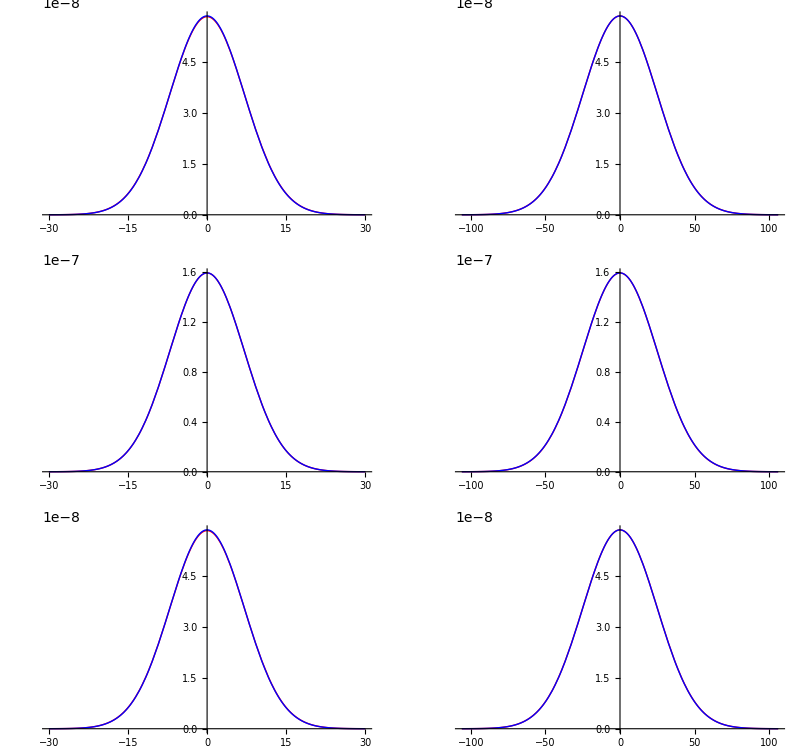
{-Graphics-,-Graphics-}

```mathematica
cs[1]=caseStudy[resolution,{0,0,0Degree},450]
```

```mathematica
cs[2]=caseStudy[resolution,{0,0,18Degree},450]
```

0.01 0.00194019 -0.0032492

$Aborted

```mathematica
cs[3]=caseStudy[resolution,{300,0,0Degree},450]
```

0.01 0.0008 0.

$Aborted

0.00692536 0.00102428 -0.00117776

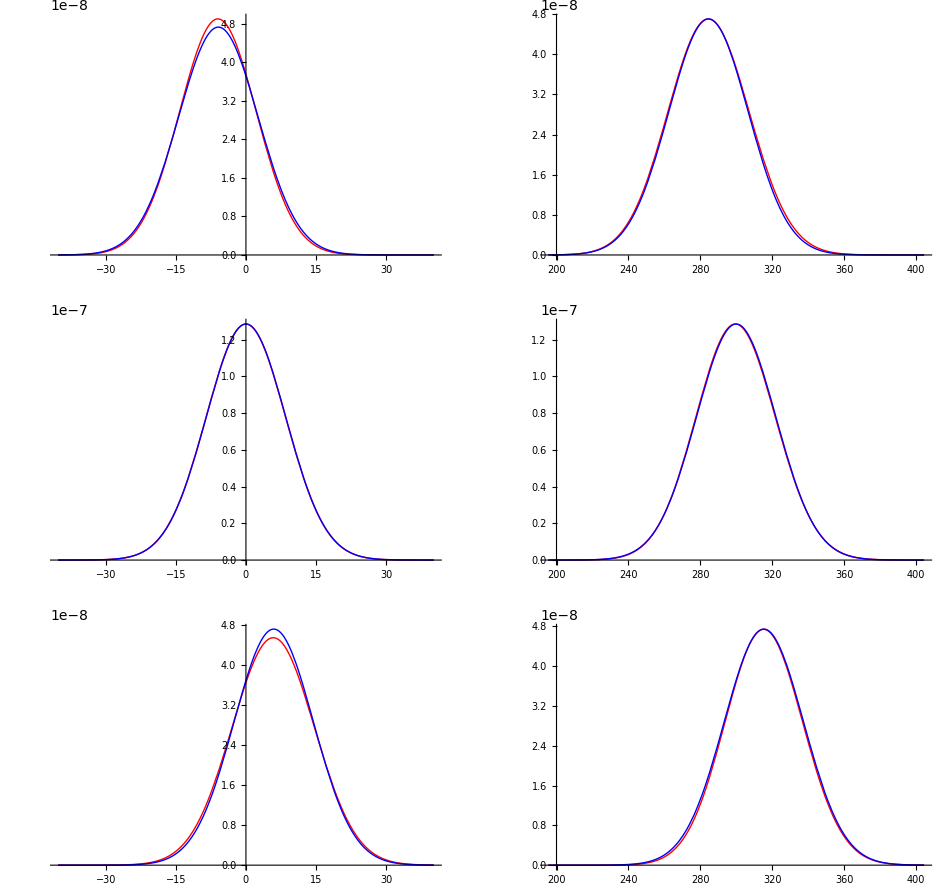
{-Graphics-,-Graphics-}

```mathematica
cs[4]=caseStudy[resolution,{300,0,10Degree},450]
```

```mathematica
Do[Export["cs_ev"<>ToString[i]<>".eps",cs[i][[1]],"EPS"];
Export["cs_pl"<>ToString[i]<>".eps",cs[i][[2]],"EPS"],
{i,1,4}]
```

```mathematica
f[z_,L_,a_]:=-2 a^2 /L^2 z^2 + 2 a^2/L z + 1/2 (1+a^2)
```

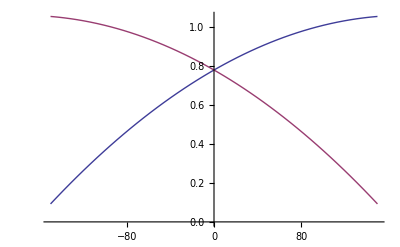

```mathematica
Plot[{f[z,350,Sqrt[1.25^2-1]],f[-z,350,Sqrt[1.25^2-1]]},{z,-150,150}]
```

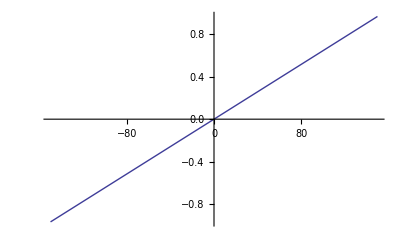

```mathematica
Plot[{f[z,350,Sqrt[1.25^2-1]]-f[-z,350,Sqrt[1.25^2-1]]},{z,-150,150}]
```